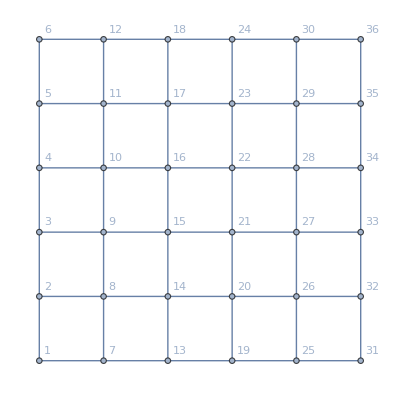

```mathematica
g= GridGraph[{6,6}, VertexLabels->Automatic]
```

```mathematica
glst = EdgeList[g]
```

{1<->2,1<->7,2<->3,2<->8,3<->4,3<->9,4<->5,4<->10,5<->6,5<->11,6<->12,7<->8,7<->13,8<->9,8<->14,9<->10,9<->15,10<->11,10<->16,11<->12,11<->17,12<->18,13<->14,13<->19,14<->15,14<->20,15<->16,15<->21,16<->17,16<->22,17<->18,17<->23,18<->24,19<->20,19<->25,20<->21,20<->26,21<->22,21<->27,22<->23,22<->28,23<->24,23<->29,24<->30,25<->26,25<->31,26<->27,26<->32,27<->28,27<->33,28<->29,28<->34,29<->30,29<->35,30<->36,31<->32,32<->33,33<->34,34<->35,35<->36}

```mathematica
forT1 = {8<->9, 9<->10,10<->11,20<->21,21<->22,22<->23 };
forT2 = {9<->15, 15<->21,21<->27,11<->17,17<->23,23<->29 };
forT3 = {13<->14, 14<->15,15<->16,26<->27,27<->28,28<->29 };
forT4={8<->14, 14<->20,20<->26,10<->16,16<->22,22<->28 };
```

```mathematica
glst =If[MemberQ[forT1, #],t1[t],If[MemberQ[forT2, #],t2[t],If[MemberQ[forT3, #],t3[t],If[MemberQ[forT4, #],t4[t],RandomInteger[{1,20}]]]]]& /@glst
```

{16,20,3,5,8,12,13,9,10,15,20,3,2,If[Mod[1/2 (-1+t-Mod[-1+t,2]),2]==0,t1Val,0],If[Mod[1/5 (-1+t-Mod[-1+t,5]),2]==0,t4Val,0],If[Mod[1/2 (-1+t-Mod[-1+t,2]),2]==0,t1Val,0],If[Mod[1/3 (-1+t-Mod[-1+t,3]),2]==0,t2Val,0],If[Mod[1/2 (-1+t-Mod[-1+t,2]),2]==0,t1Val,0],If[Mod[1/5 (-1+t-Mod[-1+t,5]),2]==0,t4Val,0],20,If[Mod[1/3 (-1+t-Mod[-1+t,3]),2]==0,t2Val,0],8,If[Mod[1/4 (-1+t-Mod[-1+t,4]),2]==0,t3Val,0],11,If[Mod[1/4 (-1+t-Mod[-1+t,4]),2]==0,t3Val,0],If[Mod[1/5 (-1+t-Mod[-1+t,5]),2]==0,t4Val,0],If[Mod[1/4 (-1+t-Mod[-1+t,4]),2]==0,t3Val,0],If[Mod[1/3 (-1+t-Mod[-1+t,3]),2]==0,t2Val,0],13,If[Mod[1/5 (-1+t-Mod[-1+t,5]),2]==0,t4Val,0],14,If[Mod[1/3 (-1+t-Mod[-1+t,3]),2]==0,t2Val,0],11,2,9,If[Mod[1/2 (-1+t-Mod[-1+t,2]),2]==0,t1Val,0],If[Mod[1/5 (-1+t-Mod[-1+t,5]),2]==0,t4Val,0],If[Mod[1/2 (-1+t-Mod[-1+t,2]),2]==0,t1Val,0],If[Mod[1/3 (-1+t-Mod[-1+t,3]),2]==0,t2Val,0],If[Mod[1/2 (-1+t-Mod[-1+t,2]),2]==0,t1Val,0],If[Mod[1/5 (-1+t-Mod[-1+t,5]),2]==0,t4Val,0],7,If[Mod[1/3 (-1+t-Mod[-1+t,3]),2]==0,t2Val,0],9,17,11,If[Mod[1/4 (-1+t-Mod[-1+t,4]),2]==0,t3Val,0],19,If[Mod[1/4 (-1+t-Mod[-1+t,4]),2]==0,t3Val,0],14,If[Mod[1/4 (-1+t-Mod[-1+t,4]),2]==0,t3Val,0],19,20,1,12,17,7,16,19,7}

```mathematica
t1Val=RandomInteger[{1,20}];
t2Val=RandomInteger[{1,20}];
t3Val=RandomInteger[{1,20}];
t4Val=RandomInteger[{1,20}];
```

```mathematica
t1[t_]:=If[Mod[ (t-1 -Mod[t-1, 2])/2,2]==0,t1Val,0];
t2[t_]:=If[Mod[ (t-1 -Mod[t-1,3])/3,2]==0,t2Val,0];
t3[t_]:=If[Mod[ (t-1 -Mod[t-1, 4])/4,2]==0,t3Val,0];
t4[t_]:=If[Mod[ (t-1 -Mod[t-1, 5])/5,2]==0,t4Val,0];
```

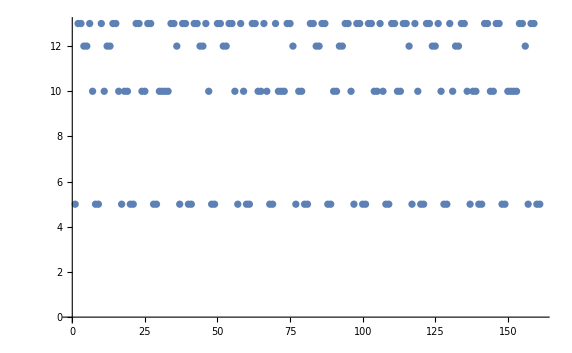

```mathematica
ListPlot[Table[FindMaximumFlow[ GridGraph[{6,6}, VertexLabels->Automatic, EdgeCapacity->glst/.t->t0], 36, 1],{t0, 0, 160}]]
```